```mathematica
Clear[ReadPlantri2];
```

```mathematica
SortEdge2[e_]:=If[OrderedQ[{e[[1]],e[[2]]}],e,UndirectedEdge[e[[2]],e[[1]]]]
```

```mathematica
ReadPlantri2[fileName_, from_,to_]:=Block[{file,vertices,result={},header,i, next,v, bigresult={},fileLength,currentPos, currentGraph=1},
PrintTemporary["Reading " <> fileName];
file=OpenRead[fileName,BinaryFormat->True];
(* read header *)
For[i=1,i≤StringLength[">>planar_code<<"],i++,
header=BinaryRead[file];
];
vertices=BinaryRead[file];
fileLength=FileByteCount[fileName];
Monitor[
While[vertices=!=EndOfFile && currentGraph<=to,
result={};
For[v=1,v≤vertices,v++,
next=BinaryRead[file];
While[next ≠ 0,
AppendTo[result,SortEdge2[UndirectedEdge[v,next]]];
next=BinaryRead[file];
];
];
If[from≤currentGraph≤to,
AppendTo[bigresult,DeleteDuplicates[result]]
];
currentGraph++;
vertices=BinaryRead[file];
currentPos=StreamPosition[file]
],
{currentGraph,ProgressIndicator[currentGraph,{0,to}],Round[(currentGraph/to)*100,.01]}
];
Close[file];
PrintTemporary["Done. " <> ToString[Length[bigresult]]];
bigresult
]
```

```mathematica
Clear[fifteen];fifteen=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",1000];Graph[fifteen[[1]],VertexLabels->"Name",GraphLayout->"CircularEmbedding"]
```

Graph[D:\cygwin64\home\alfre\plantri15.txt,VertexLabels→Name,GraphLayout→CircularEmbedding]

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",10]},
Flatten[
Monitor[
Table[
Map[PartitionType[SymbolToSets[#]]&,FindFullFormula4[Graph[set[[kk]]]]],{kk,Length[set]}],
ProgressIndicator[kk,{0,Length[set]}]
],
1]//Tally//Sort
]
```

VertexList::graph: A graph object is expected at position 1 in VertexList[Graph[D:\cygwin64\home\alfre\plantri15.txt]].

Table::iterb: Iterator {v,VertexList[Graph[D:\cygwin64\home\alfre\plantri15.txt]]} does not have appropriate bounds.

FindClique::graph: A graph object is expected at position 1 in FindClique[Graph[D:\cygwin64\home\alfre\plantri15.txt]].

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]].

Part::partw: Part 2 of GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]] does not exist.

Part::pkspec1: The expression pos1 cannot be used as a part specification.

Part::pkspec1: The expression pos2 cannot be used as a part specification.

Part::pkspec1: The expression pos1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]].

FindClique::graph: A graph object is expected at position 1 in FindClique[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]].

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]]].

Part::partw: Part 2 of GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]],GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]]].

FindClique::graph: A graph object is expected at position 1 in FindClique[EdgeAdd[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]],GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]]]].

General::stop: Further output of FindClique::graph will be suppressed during this calculation.

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[EdgeAdd[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]],GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]]]].

General::stop: Further output of GraphComplement::graph will be suppressed during this calculation.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[EdgeAdd[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]],GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]]]]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[EdgeAdd[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]],GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]]],GraphComplement[EdgeAdd[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]],GraphComplement[EdgeAdd[Graph[D:\cygwin64\home\alfre\plantri15.txt],GraphComplement[Graph[D:\cygwin64\home\alfre\plantri15.txt]]]]]]].

General::stop: Further output of EdgeAdd::graph will be suppressed during this calculation.

$Aborted

```mathematica
.
```

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",10]},
Flatten[
Monitor[
Table[
FindFullFormula4[Graph[set[[kk]]]],{kk,Length[set]}],
ProgressIndicator[kk,{0,Length[set]}]
],
1]//Tally//Sort
]
```

{{v1acefx257x368bx49d,1},{v1acex257fx368bx49d,3},{v1adfx257x368cx49be,1},{v1bdex257fx368ax49c,1},{v1bdfx257ex368ax49c,1},{v1bdfx257x368acx49e,1},{v1bdx257ex368ax49cf,1},{v1bdx257fx368aex49c,1}}

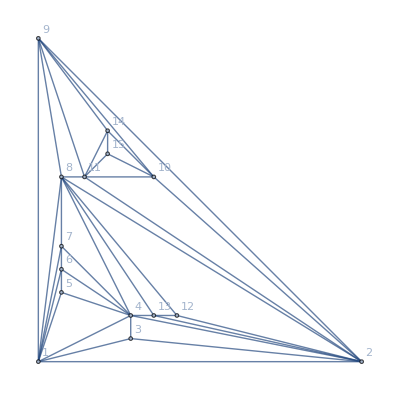
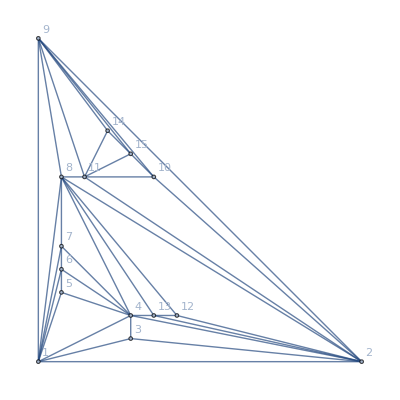
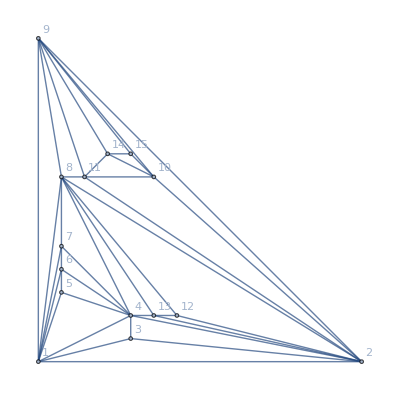
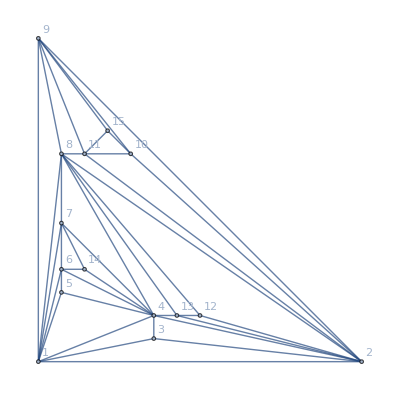
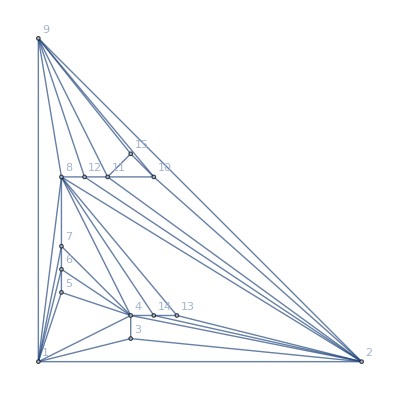
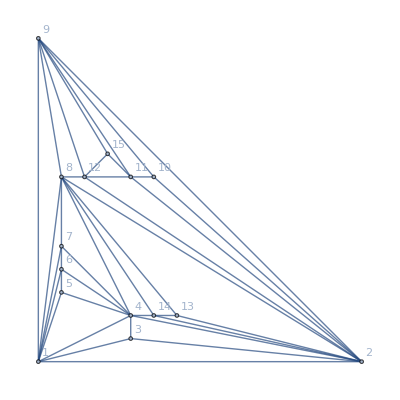
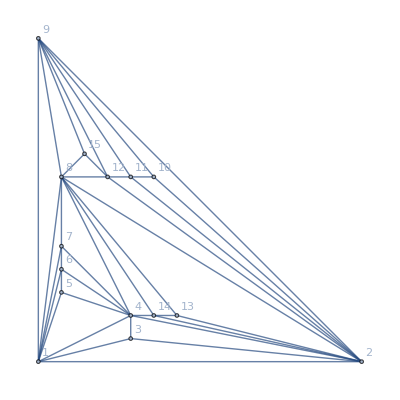
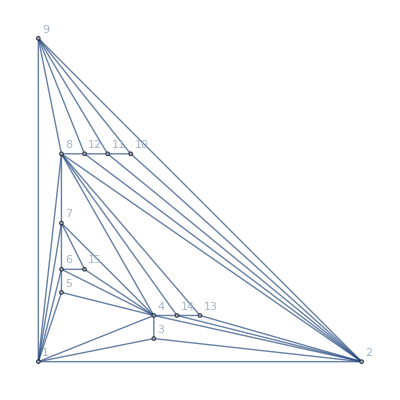
{{-Graphics-1,1},{-Graphics-1,1},{-Graphics-1,1},{-Graphics-1,1},{-Graphics-1,1},{-Graphics-1,1},{-Graphics-1,1},{-Graphics-1,1},{-Graphics-1,1},{-Graphics-1,1}}

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",10]},
Flatten[
Monitor[
Table[
With[{g=Graph[set[[kk]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]},
Labeled[g,ChromaticPolynomial[g,4]/24]
],{kk,Length[set]}],
ProgressIndicator[kk,{0,Length[set]}]
],
1]//Tally//Sort
]
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

False

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",5000]},
Flatten[
Monitor[
ParallelTable[
With[{g=Graph[set[[kk]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]},
ChromaticPolynomial[g,4]/24
],{kk,Length[set]}],
{ProgressIndicator[kk,{0,Length[set]}],N[kk/Length[set]*100,2],"%"}
],
1]//Tally//Sort
]
```

{{1,5000}}

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",100000+1,100000+100]},
Flatten[
Monitor[
Table[
With[{g=Graph[set[[kk]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]},
ChromaticPolynomial[g,4]/24
],{kk,Length[set]}],
{ProgressIndicator[kk,{0,Length[set]}],Round[kk/Length[set]*100,.01],"%"}
],
1]//Tally//Sort
]
```

{{1,100}}

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",200000+1,200000+100]},
Flatten[
Monitor[
Table[
With[{g=Graph[set[[kk]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]},
ChromaticPolynomial[g,4]/24
],{kk,Length[set]}],
{ProgressIndicator[kk,{0,Length[set]}],Round[kk/Length[set]*100,.01],"%"}
],
1]//Tally//Sort
]
```

{{1,100}}

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",0+1,0+100]},
Flatten[
Monitor[
Table[
With[{g=Graph[set[[kk]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]},
ChromaticPolynomial[g,4]/24
],{kk,Length[set]}],
{ProgressIndicator[kk,{0,Length[set]}],Round[kk/Length[set]*100,.01],"%"}
],
1]//Tally//Sort
]
```

{{1,100}}

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",800000+1,800000+100]},
Tally[
Flatten[
Monitor[
Table[
With[{g=Graph[set[[kk]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]},
ChromaticPolynomial[g,4]/24
],{kk,Length[set]}],
{ProgressIndicator[kk,{0,Length[set]}],Round[kk/Length[set]*100,.01],"%"}
],
1]
]
]
```

Reading D:\cygwin64\home\alfre\plantri15.txt

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",800000+1,800000+500]},
Tally[
Flatten[
Monitor[
Table[ges
With[{g=Graph[set[[kk]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]},
ChromaticPolynomial[g,4]/24
],{kk,Length[set]}],
{ProgressIndicator[kk,{0,Length[set]}],Round[kk/Length[set]*100,.01],"%"}
],
1]
]
]
```

```mathematica
{{5,500}}{{
```

```mathematica
With[
{set=ReadPlantri2["D:\\cygwin64\\home\\alfre\\plantri15.txt",805000+1,805000+500]},
Tally[
Flatten[
Monitor[
Table[
With[{g=Graph[set[[kk]],GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]},
ChromaticPolynomial[g,4]/24
],{kk,Length[set]}],
{ProgressIndicator[kk,{0,Length[set]}],Round[kk/Length[set]*100,.01],"%"}
],
1]
]
]
```

{{5,497},{20,2},{25,1}}